#### Mathematica file to compute New Physics contributions to g-2. Acknowledgments should be referred to: Farinaldo S. Queiroz and William Shepherd [arxiv:1403.2309] and M Lindner, M Platscher, FS Queiroz, https://doi.org/10.1016/j.physrep.2017.12.001 [ arXiv:1610.06587v2]

The reader should straightforwardly use this mathematica file to compute the total contribution of a generic model to the muon magnetic moment at 1-loop level. Plots are also available. We have closely followed the notation of our paper arxiv.

New Physics Contribution to (g-2)_μ

Global Parameters. 
Masses of the SM particles in GeV units.

```mathematica
mμ=0.105; (*Muon mass*)
mν=0.1*10^-9; (*Neutrino mass*) 
g=0.65; (*SM coupling constant*)
SW2=0.231; SW=Sqrt[SW2]; CW=Sqrt[1-SW2]; (*Weinberg angle relations*)
t=Sqrt[(SW2)/(1-4*SW2)]; (*Because in the model e=gt/(√(1+4 t^2))=gSw*)
a=0.01; (*Used in 10.1103/PhysRevD.51.3865*)
```

Experimental Bounds
based on (antigos):
Current Bound: (295 ± 81) x 10^-11;
Projected Bound:  (295 ± 34) x 10^-11;

based on (novos):
Current Bound: (261 ± 78) x 10^-11;
Projected Bound:  (261± 34) x 10^-11;

```mathematica
BoundProjectedup=Table[{x,295*10^-11},{x,1,10000,1}];
BoundProjecteddown=Table[{x,227*10^-11},{x,1,10000,1}];
BoundCurrenteup=Table[{x,339*10^-11},{x,1,10000,1}];
BoundCurrentdown=Table[{x,183*10^-11},{x,1,10000,1}];
sigmaCurrent=Table[{x,78*10^-11},{x,1,10000,1}];
sigmaProjected=Table[{x,34*10^-11},{x,1,10000,1}];
```

#### Z’ boson (n=2 in the model)

L ~ g_v Z_nρ μ̄ γ^ρ μ + g_a Z_nρ μ̄ γ^ργ^5μ;  Z_((n=2)ρ)=Z'_ρ

```mathematica
A=3+4*t^2+(7+4*t^2)*a^2;B=-2*((1+3*t^2)+2*(4+9*t^2)*a^2);C1=8*(1+4*t^2)*a^2;
Theta=ArcCos[(2*A^3+9*A*B+27*C1)/(2*(A^2+3*B)^(3/2))];
λ2=1/3*(A+2*(A^2+3*B)^(1/2) )*Cos[(4*π+Theta)/3];
w2=1;

Dn=2*(7+5*a^2)-(3+13*a^2)*λ2+2*λ2^2;
x2=-(2*a^2)/t*(1-3*t^2+(1-t^2)*a^2-(1-2*t^2)*λ2)/Dn*w2;
y2=1/Dn*1/(√3*t)*(2*(2+t^2)*a^2-10*a^4*t^2-(1+(1-4*t^2)*a^2)*λ2)*w2;
z2=1/Dn*1/(√6*t)*(8*(2+t^2)*a^2+  4*(3+2* t^2)*a^4-4*(1+2*(2+t^2)*a^2* λ2+3*λ2^2))*w2;
gv9=1/2*( -CW*(-x2+1/(√3)*y2+1/(√6)*z2+4/3*w2*t)+4/3*CW*w2*t-3/(√6)*z2 )*g/(2*CW) ;
ga9=1/2*( +CW*(-x2+1/(√3)*y2+1/(√6)*z2+4/3*w2*t)-4/3*CW*w2*t-3/(√6)*z2 )*g/(2*CW) ;
```

```mathematica
mf9=mμ; ϵ9=mf9/mμ;λ9=mμ/MZp;
ΔaZp=Table[{MZp,(gv9^2*mμ^2)/(8*π^2*MZp^2)*NIntegrate[(2*x*(1-x)*(x-2+2*ϵ9)+λ9^2*x^2*(1-ϵ9)^2*(1-x+ϵ9))/((1-x)*(1-λ9^2*x)+ϵ9^2*λ9^2*x),{x,0,1}] 
+ (ga9^2*mμ^2)/(8*π^2*MZp^2)*NIntegrate[(2*x*(1-x)*(x-2-2*ϵ9)+λ9^2*x^2*(1+ϵ9)^2*(1-x-ϵ9))/((1-x)*(1-λ9^2*x)+ϵ9^2*λ9^2*x),{x,0,1}] },{MZp,100,10000,100}];
```

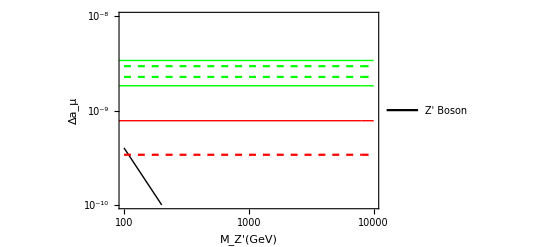

```mathematica
(* USe the commands below in case the Neutral Vector Boson contribution of your particular model is negative. This is only necessary in case the reader is interested in using the ListLogLogPlot below as we did.*)

size9=Dimensions[ΔaZp];
ΔaZpnew=Table[{ΔaZp[[i,1]],-ΔaZp[[i,2]]},{i,1,size9[[1]]}];

(*Plot of the Neutral Vector Boson contribution to Subscript[(g-2), μ] as a function of its mass*)

ListLogLogPlot[{ΔaZpnew,BoundCurrenteup,BoundCurrentdown,BoundProjectedup,BoundProjecteddown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,10000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[M,Z'][GeV]],12],Style[HoldForm[Subscript[Δa,μ]],15]},PlotLegends->Placed[LineLegend[{"Z' Boson"}],{0.5,0.9}]]
```

#### Z_N boson (n=0 in the model)

L ~ g_v Z_nρ μ̄ γ^ρ μ + g_a Z_nρ μ̄ γ^ργ^5μ;  Z_((n=0)ρ)=Z_Nρ

```mathematica
λ0=1/3*(A+2*(A^2+3*B)^(1/2) )*Cos[Theta/3];
w0=1;

D0=2*(7+5*a^2)-(3+13*a^2)*λ0+2*λ0^2;
x0=-(2*a^2)/t*(1-3*t^2+(1-t^2)*a^2-(1-2*t^2)*λ0)/D0*w0;
y0=1/D0*1/(√3*t)*(2*(2+t^2)*a^2-10*a^4*t^2-(1+(1-4*t^2)*a^2)*λ0)*w0; 
z0=1/D0*1/(√6*t)*(8*(2+t^2)*a^2+  4*(3+2* t^2)*a^4-4*(1+2*(2+t^2)*a^2* λ0+3*λ0^2))*w0;
gv19=1/2*( -CW*(-x0+1/(√3)*y0+1/(√6)*z0+4/3*w0*t)+4/3*CW*w0*t-3/(√6)*z0 )*g/(2*CW) ;
ga19=1/2*( +CW*(-x0+1/(√3)*y0+1/(√6)*z0+4/3*w0*t)-4/3*CW*w0*t-3/(√6)*z0 )*g/(2*CW);
```

```mathematica
mf19=mμ; ϵ19=mf19/mμ;λ19=mμ/MZN;
ΔaZN=Table[{MZN,(gv19^2*mμ^2)/(8*π^2*MZN^2)*NIntegrate[(2*x*(1-x)*(x-2+2*ϵ19)+λ19^2*x^2*(1-ϵ19)^2*(1-x+ϵ19))/((1-x)*(1-λ19^2*x)+ϵ19^2*λ19^2*x),{x,0,1}] 
+ (ga19^2*mμ^2)/(8*π^2*MZN^2)*NIntegrate[(2*x*(1-x)*(x-2-2*ϵ19)+λ19^2*x^2*(1+ϵ19)^2*(1-x-ϵ19))/((1-x)*(1-λ19^2*x)+ϵ19^2*λ19^2*x),{x,0,1}] },{MZN,100,10000,100}];
```

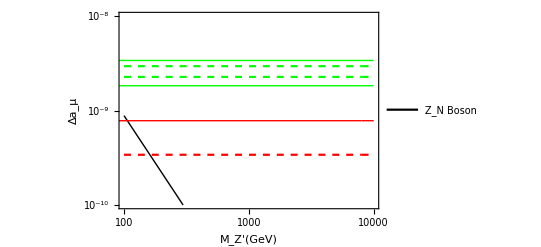

```mathematica
size19=Dimensions[ΔaZN];
ΔaZNnew=Table[{ΔaZN[[i,1]],-ΔaZN[[i,2]]},{i,1,size19[[1]]}];
ListLogLogPlot[{ΔaZNnew,BoundCurrenteup,BoundCurrentdown,BoundProjectedup,BoundProjecteddown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,10000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[M,Z'][GeV]],12],Style[HoldForm[Subscript[Δa,μ]],15]},PlotLegends->Placed[LineLegend[{"Z_N Boson"}],{0.5,0.9}]]
```

#### Charged Vector Boson . There are two V^+ in this model. So I added a factor of 2.

L ~ g_(1v) V_(1ρ)^+OverBar[ν^c] γ^ρ μ + g_(1A) V_(1ρ)^+OverBar[ν^c] γ^ργ^5μ +g_(2v) V_(2ρ)^+OverBar[μ^c] γ^ρν+ g_(2A) V_(2ρ)^+OverBar[μ^c]γ^ργ^5ν

```mathematica
ϵ10=mν/mμ; λ10=mμ/MV;gv10=g/(2*√2);ga10=g/(2*√2);
ΔaChargedVec=Table[{MV,2*(-(gv10^2*mμ^2)/(8*π^2*MV^2)*NIntegrate[(-2*x^2*(1+x-2*ϵ10)+λ10^2*x*(1-x)*(1-ϵ10)^2*(x+ϵ10))/(ϵ10^2*λ10^2*(1-x)*(1-ϵ10^-2*x)+x),{x,0,1}]-(ga10^2*mμ^2)/(8*π^2*MV^2)*NIntegrate[(-2*x^2*(1+x+2*ϵ10)+λ10^2*x*(1-x)*(1+ϵ10)^2*(x-ϵ10))/(ϵ10^2*λ10^2*(1-x)*(1-ϵ10^-2*x)+x),{x,0,1}])},{MV,100,10000,100}];
```

```mathematica
(* USe the commands below in case the Singly Charged Vector Boson contribution of your particular model is negative. This is only necessary in case the reader is interested in using the ListLogLogPlot below as we did.*)

(*size10=Dimensions[ΔaChargedVec];
ΔaChargedVecnew=Table[{ΔaChargedVec[[i,1]],-ΔaChargedVec[[i,2]]},{i,1,size10[[1]]}];*)
```

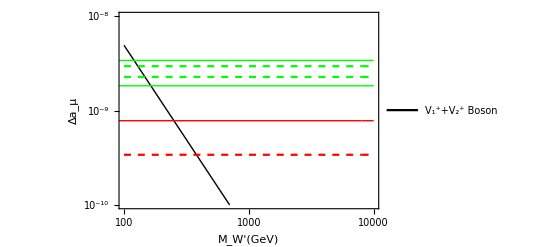

```mathematica
(*Plot of the Charged Vector Boson contribution to Subscript[(g-2), μ] as a function of its mass*)

plot10=ListLogLogPlot[{ΔaChargedVec,BoundCurrenteup,BoundCurrentdown,BoundProjectedup,BoundProjecteddown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,10000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[M,W'][GeV]],12],Style[HoldForm[Subscript[Δa,μ]],15]},PlotLegends->Placed[LineLegend[{"V_1^++V_2^+ Boson"}],{0.6,0.9}]]
```

### Doubly Charged Boson

L ~ g_VU_ρ^(++)OverBar[μ^c] γ^ρ μ +g_AU_μ^(++)OverBar[μ^c] γ^μγ^5 μ

```mathematica
mf12=mμ;ϵ12=mf12/mμ; λ12=mμ/MU;
gv12=0;
ga12=g/(2*√2); 
ΔaDChargedVec=Table[{MU,8*((gv12^2*mμ^2)/(8*π^2*MU^2)*NIntegrate[(-2*x^2*(1+x-2*ϵ12)+λ12^2*x*(1-x)*(1-ϵ12)^2*(x+ϵ12))/(ϵ12^2*λ12^2*(1-x)*(1-ϵ12^-2*x)+x),{x,0,1}]+(ga12^2*mμ^2)/(8*π^2*MU^2)*NIntegrate[(-2*x^2*(1+x+2*ϵ12)+λ12^2*x*(1-x)*(1+ϵ12)^2*(x-ϵ12))/(ϵ12^2*λ12^2*(1-x)*(1-ϵ12^-2*x)+x),{x,0,1}])-
(-4)*((gv12^2*mμ^2)/(8*π^2*MU^2)*NIntegrate[(2*x*(1-x)*(x-2+2*ϵ12)+λ12^2*x^2*(1-ϵ12)^2*(1-x+ϵ12))/((1-x)*(1-λ12^2*x)+ϵ12^2*λ12^2*x),{x,0,1}] 
+ (ga12^2*mμ^2)/(8*π^2*MU^2)*NIntegrate[(2*x*(1-x)*(x-2-2*ϵ12)+λ12^2*x^2*(1+ϵ12)^2*(1-x-ϵ12))/((1-x)*(1-λ12^2*x)+ϵ12^2*λ12^2*x),{x,0,1}] )

},{MU,100,10000,100}];
```

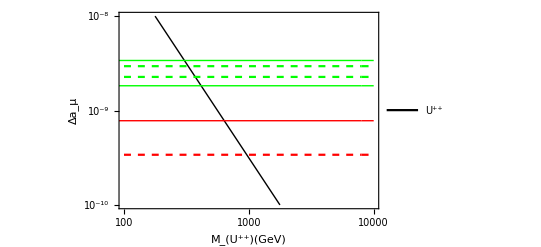

```mathematica
(* USe the commands below in case the Doubly Charged Vector Boson contribution of your particular model is negative. This is only necessary in case the reader is interested in using the ListLogLogPlot below as we did.*)

size12=Dimensions[ΔaDChargedVec];
ΔaDChargedVecnew=Table[{ΔaDChargedVec[[i,1]],-ΔaDChargedVec[[i,2]]},{i,1,size12[[1]]}];

(*Plot of the Doubly Charged Vector Boson contribution to Subscript[(g-2), μ] as a function of its mass*)

plot12=ListLogLogPlot[{ΔaDChargedVecnew,BoundCurrenteup,BoundCurrentdown,BoundProjectedup,BoundProjecteddown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,10000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[M,"U^(++)"][GeV]],12],Style[HoldForm[Subscript[Δa,μ]],15]},PlotLegends->Placed[LineLegend[{"U^(++)"}],{0.6,0.2}]]
```

COMBINED CONTRIBUTIONS OF SPIN 0 PARTICLES

```mathematica
plottotal1=ListLogLogPlot[{ΔaDChargedVecnew,ΔaChargedVec,ΔaZpnew,ΔaZNnew,BoundCurrenteup,BoundProjectedup,sigmaCurrent,sigmaProjected,BoundCurrentdown,BoundProjecteddown},PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick],Directive[Gray,Thick],Directive[Orange,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed],Directive[Green,Thick],Directive[Green,Dashed]},Joined->True,PlotRange->{{100,2000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm["Mass "[GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->LineLegend[{"U^(++) x (-1)","V_1^++V_2^+","Z' x (-1)","Z_N x (-1)","Δa_μ Current","Δa_μ Projected","1σ Bound Current","1σ Bound Projected"}],PlotLabel->Style["SU(4)_L⊗ U(1)_X Model",14,Black,Bold]]
```

```mathematica
sizetotal=Dimensions[ΔaChargedVec]
```

{100,2}

```mathematica
Totalcontri=Table[{ΔaChargedVec[[i,1]],ΔaChargedVec[[i,2]]+ΔaZp[[i,2]]+ΔaZN[[i,2]]+ΔaDChargedVec[[i,2]]},{i,1,sizetotal[[1]]}];
Totalcontrinew=Table[{Totalcontri[[i,1]],-Totalcontri[[i,2]]},{i,1,sizetotal[[1]]}];
```

```mathematica
plottotal10=ListLogLogPlot[{Totalcontrinew,BoundCurrenteup,BoundProjectedup,sigmaCurrent,sigmaProjected,BoundCurrentdown,BoundProjecteddown},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Dashed],Directive[Red,Thick],Directive[Red,Dashed],Directive[Green,Thick],Directive[Green,Dashed]},Joined->True,PlotRange->{{200,2000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[ Mass[GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->LineLegend[{"Total(-1)","\!\(\*SubscriptBox[\(Δa\), \(μ\)]\) Current","\!\(\*SubscriptBox[\(Δa\), \(μ\)]\) Projected","1σ Bound Current","1σ Bound Projected"}],PlotLabel->Style["SU(4)_L⊗ U(1)_X Model",14,Black,Bold]]
```